# PRTL01 - First case for PRTL

Conventional line model and grounding, concave lightning discharge

Using package “prtl” for shared functions

```mathematica
Clear["Global`*"]
```

```mathematica
(*
General options and configurations
*)
Print["Current dir: ", SetDirectory[NotebookDirectory[]]]
<< prtl.m
markers1={{Thick,Darker@Red,Line[{{1,0},{3,0}}]}};
markers2={{Thick,Darker@Blue, Dashed,Line[{{1,0},{3,0}}]}};
markers3={{Thick,Darker@Green, Dotted,Line[{{1,0},{3,0}}]}};
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined->True,PlotStyle-> {markers1,markers2,markers3},
Axes-> False,Frame-> True,PlotRange->All];
ϵ=8.854 10^-12;
μ= 4.0 π 10^-7;
```

Current dir: /home/ck/programas/PRTL

```mathematica
(* 
Internal impedance for tubular conductors
*)
ZintTubo[Omega_,Rhoc_, rf_, rint_, Mur_: 1, Mu_: (4.*Pi)/10^7] := 
       Module[{r},  With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]],ri=rint+10^-6}, 
        With[{Den = BesselK[1,Etac*ri]*BesselI[1,Etac*rf]-BesselK[1,Etac*rf]*BesselI[1,Etac*ri], 
             Num =  BesselK[1,Etac*ri]*BesselI[0,Etac*rf]+BesselK[0,Etac*rf]*BesselI[1,Etac*ri]}, 
        ((Rhoc*Etac)*Num)/((2*Pi*rf)*Den)]]]
```

```mathematica
(*
Internal inpedance for cylindrical conductors
Considering μr=80 for steel cables
*)    
Zin[Omega_, Rhopr_, rpr_, Mur_:80, Mu_:(4*Pi)/10^7] := 
    With[{Etapr = Sqrt[(I*Omega*Mu*Mur)/Rhopr]}, 
         ((Etapr*Rhopr)*BesselI[0, Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]
```

```mathematica
ynlt[Z_,Y_,length_]:=Module[{Z1=Z,Y1=Y,eval,evect,d,Tv,Tvi,hm,Am,Bm,y11,y12},{eval,evect}=Eigensystem[N[Z1.Y1]];
d=Sqrt[eval];
Tv=Transpose[evect];
Tvi=Inverse[Transpose[evect]];
hm=Exp[-d*length];
Am=d*(1+hm^2)/(1-hm^2);
Bm=-2.0*d*hm/(1-hm^2);
y11=N[Inverse[Z1]].Tv.DiagonalMatrix[Am].Tvi;
y12=N[Inverse[Z1]].Tv.DiagonalMatrix[Bm].Tvi;
{y11,y12}];
```

## Network configuration

```mathematica
nfases=3;
npr=1;
(* Phase conductors - ACSR Penguin *)
Rdcf=0.17*10^-3 ;
rf=7.1501*10^-3;
rint=2.3876*10^-3;
Rdc=35.356020838304296*10^-5 ;
(* Ground wire - 3/8" EHS *)
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
xc={-3.8,3.8,-3.8,0};
yc={21.2, 23.1, 21.2+3.8, 21.2+3.8+5.6 };
fl={9.25, 9.25, 9.25 ,4.7}; (* conductors sag *)
σs=3 10.0^-3;(* Ground adimittance *)
ϵr=10.0;(* Ground permitivitty *)
compr=400.0;(* Span length *)
(* 
Tower model: lumped elements 
*)
Zc1=130.0;
Zc2=185.0;
Zc3=240.0;
Zc4=290.0;
Zg=11.6;
tMax=0.000020;
yc=yc-2/3 fl;
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.20]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> Automatic,PlotRange->{{-10,10},{5,Max[yc]+3}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 450,FrameLabel->{Style["Width [m]",16],Style["Height [m]",16]}]
```

-Graphics-

```mathematica
ncond=Length[xc];
nc = ncond;
ρc=Rdc* π* (rf^2-rint^2);
ρpr=Rdcpr*π *rpr^2;
(* Frequency range *)
n=4*1024;
T=tMax*2.4;
c=-Log[0.001]/T;
dt=N[T/n];
Print["dt = ", dt, " s"]
dw=2. Pi/(n*dt);
Print["df = ", dw/(2 Pi)," Hz"]
tfreq=dt Range[0,n-1] ;
ntfreq=Length[tfreq];
kk=Range[0,n/2];
sk=-I c+ dw kk;
sigma[j_]=Cos[π j/(n)]^2;
nf=nfsk2=Length[sk];
Print["nf = ", nf]
```

dt = 1.17188×10^-8 s

df = 20833.3 Hz

nf = 2049

```mathematica
ynlt1f[ω_,zc_,vpu_,len_]:=Module[{c=3.0*10^8,v, yc,h,y1,y2},
yc=1/zc;
v= vpu*c;
h=Exp[-I ω len/v];
y1=yc*(1+h^2)/(1-h^2);
y2=-2yc*h/(1-h^2);
{y1,y2}
]
```

```mathematica
twrsmplmdl[yt1s_,yt1m_,yt2s_,yt2m_,yt3s_,yt3m_,yt4s_,yt4m_,i_,j_,k_,l_,m_,s_]:=Module[{aux1,aux2,aux3,aux4},
aux1=SparseArray[{{i,i}->yt1s, {i,j}->yt1m,{j,i}->yt1m,{j,j}->yt1s},{s,s}];
aux2=SparseArray[{{j,j}->yt2s, {j,k}->yt2m,{k,j}->yt2m,{k,k}->yt2s},{s,s}];
aux3=SparseArray[{{k,k}->yt3s, {k,l}->yt3m,{l,k}->yt3m,{l,l}->yt3s},{s,s}];
aux4=SparseArray[{{l,l}->yt4s, {l,m}->yt4m,{m,l}->yt4m,{m,m}->yt4s},{s,s}];
aux1+aux2+aux3+aux4]
```

```mathematica
nILT[F_,t_,Δt_,c_]:=Module[{nc,v},
nc=Dimensions[F][[2]];
v=Table[Exp[c t]/Δt Re[ InverseFourier[F[[All,i]],FourierParameters->{1,-1}]],{i,nc}];
Return[v]]
```

```mathematica
montaLap[m_,nfreq_]:=Module[{outlow=m,lowerhalf,upperhalf,F},
lowerhalf=Delete[outlow,nfreq];
upperhalf=Reverse[Conjugate[outlow]];
upperhalf=Delete[upperhalf,nfreq];
F =Join[lowerhalf,upperhalf];
Return[F]]
```

```mathematica
dim= 40;
```

### Current source (lightning model) Heidler function

```mathematica
inputfunction[t_,i0_?VectorQ,t1_?VectorQ,t2_?VectorQ,n_?VectorQ]:=Total@With[{η=Exp[-(t1/t2)((n t2/t1)^(1/n))]},
i0/η (((t/t1)^n)/(1+((t/t1)^n)))Exp[-t/t2]];
(* 
caso #1 - Morro do Cachimbo Station
*)
ikHeidler1={6,5,5,8,22,20};
nkHeidler1={2,3,5,9,21,2};
τ1kHeidler1={3, 3.5, 4.8, 6, 7, 70}*10.^-6;
τ2kHeidler1={76,10,30,26,23.2, 200}*10.^-6;
input=inputfunction[#1, ikHeidler1, τ1kHeidler1, τ2kHeidler1,nkHeidler1]&/@tfreq;
(* 
convertendo para o dominio da frequencia usando FFT 
*) 
inputfreq=Fourier[Exp[-c tfreq]input,FourierParameters->{1,-1}]*dt;
```

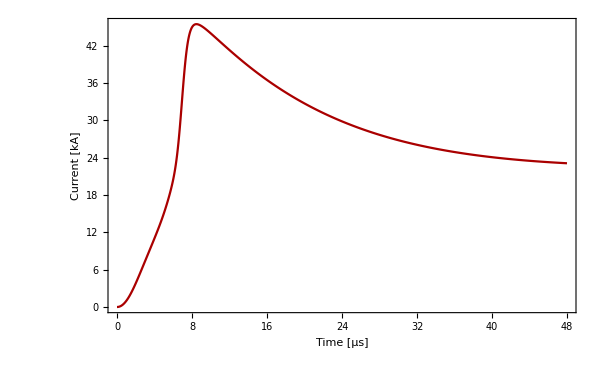
-Graphics-Input function for current source

```mathematica
v1outf1=v1outf2=v1outf3=Hmodalufreq=Hufreq=Ycufreq=λ0ufreq=Tufreq=YNodalUfreq=Table[0.,{i,nfsk2}];
Labeled[ListPlot[Transpose@{tfreq*10^6,input}, FrameLabel-> {"Time [μs]", "Current [kA]"}],"Input function for current source"]
```

```mathematica
nb=CreatePalette[ProgressIndicator[Dynamic[progress]],WindowTitle->"NLT Solver",WindowMargins->Automatic];
progress=0;
bfreq=ConstantArray[0,{dim}];

AbsoluteTiming[Do[{ω=sk[[nm]],

γs=Sqrt[ⅉ ω μ (σs+ⅉ ω ϵr ϵ)];
γar=ⅉ ω Sqrt[μ ϵ];

m=MPot[xc,yc,ncond,npr,rf,rpr];
zin=DiagonalMatrix[Table[If[i≤ ncond-npr,ZintTubo[ω,ρc,rf,rint],Zin[ω,ρpr,rpr]],{i,ncond}]];
(*
S1 matrix
*)
s1=S1[xc,yc,ncond,npr,rf,rpr,γs,γar];
 
(*
definicao de diferenca de potencial
*)
ze=zin+ⅉ ω μ/(2 π)(m+s1);
Z2= ze;
Y2=ⅉ ω 2 π ϵ Inverse[m];
(*
Yn=Ynodal[Z2,Y2,compr];
*)
{YL1,YL2}=ynlt[Z2,Y2,compr],
{YTT,aux}=ynlt[Z2,Y2,10000],
Yn=ArrayFlatten[{{YL1,YL2},{YL2,YL1}}],
Yaux=ArrayFlatten[{
{YTT+YL1,YL2,0,0,0},
{YL2, 2YL1,YL2,0,0},
{0,YL2,2YL1,YL2,0},
{0,0,YL2,2YL1,YL2},
{0,0,0,YL2,YTT+ YL1}}],

yrede=SparseArray[Flatten@Table[{i,j}-> Yaux[[i,j]],{i,Length[Yaux]},{j,Length[Yaux]}],{dim, dim}];

{yt11,yt12}=ynlt1f[ω,Zc1, .8, 8.5];
{yt21,yt22}=ynlt1f[ω,Zc2, .8, 8.5];
{yt31,yt32}=ynlt1f[ω,Zc3, .8, 8.5];
{yt41,yt42}=ynlt1f[ω,Zc4, .8, 5.6];

yg=SparseArray[{{24,24}->1/Zg, {28,28}->1/Zg,{32,32}->1/Zg,{36,36}->1/Zg,{40,40}->1/Zg}];

ytower1=twrsmplmdl[yt11,yt12,yt21,yt22,yt31,yt32,yt41,yt42,4,21,22,23,24,40];
ytower2=twrsmplmdl[yt11,yt12,yt21,yt22,yt31,yt32,yt41,yt42,8,25,26,27,28,40];
ytower3=twrsmplmdl[yt11,yt12,yt21,yt22,yt31,yt32,yt41,yt42,12,29,30,31,32,40];
ytower4=twrsmplmdl[yt11,yt12,yt21,yt22,yt31,yt32,yt41,yt42,16,33,34,35,36,40];
ytower5=twrsmplmdl[yt11,yt12,yt21,yt22,yt31,yt32,yt41,yt42,20,37,38,39,40,40],

yaug=yrede+ytower1+ytower2+ytower3+ytower4+ytower5+yg,

bfreq[[12]]=inputfreq[[nm]],

v1outf1[[nm]] =PseudoInverse[yaug].bfreq;,

progress=nm/nf;

},{nm,1,nf}]]
NotebookClose[nb];
```

General::munfl: -1/(6.67196×10^306+8.13495×10^305 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1/(7.4579×10^306+1.76584×10^307 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1/(1.35841×10^306+2.71403×10^307 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{5.65137,Null}

```mathematica
outlow1=v1outf1  Map[ sigma, kk];
F=montaLap[outlow1,nfsk2];
vf1=nILT[F,tfreq,dt,c];
```

```mathematica
{v0f1,vLf1,ifF1}={vf1[[1;;nc]],vf1[[nc+1;;2*nc]],vf1[[2*nc+1]]};
```

```mathematica
Dimensions[vf1]
```

{40,4096}

## Graphics output

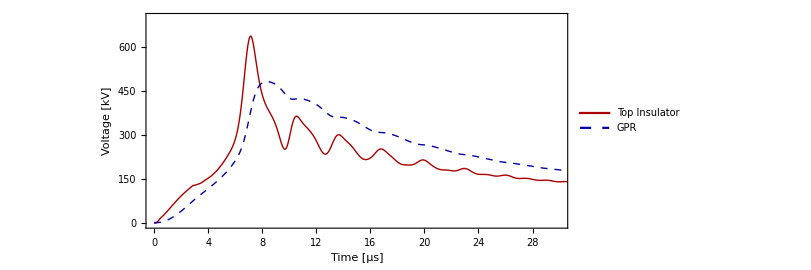

```mathematica
o1a=ListPlot[{Transpose@{tfreq *10^6,vf1[[29]]-vf1[[9]]},Transpose@{tfreq *10^6,vf1[[32]]}}, PlotRange->{{0, 30}, {-5,700}},
FrameLabel-> {"Time [μs]", "Voltage [kV]"},PlotLegends->Placed[LineLegend[{"Top Insulator","GPR"}],{.85,.85}], AspectRatio->.45]
```

```mathematica
Export["caso1.pdf", o1a]
```

caso1.pdf

```mathematica
Export["caso1.mx",{tfreq, vf1[[29]]-vf1[[9]],vf1[[32]]}]
```

caso1.mx

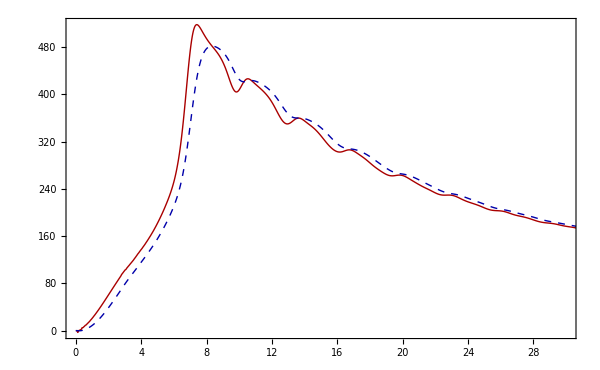

```mathematica
ListPlot[{Transpose@{tfreq *10^6,vf1[[31]]},Transpose@{tfreq *10^6,vf1[[32]]}}, PlotRange->{{0, 30}, All}]
```